```mathematica
SetDirectory["\\\\home.org.aalto.fi\\heikkie13\\data\\Documents\\work\\my research\\Howard\\encoder decoder scratches\\Mathematica"];
<<FunctionsComplexAnalysis.m;
<<FunctionsMatrixAnalysis.m;
<<FunctionsFiniteGroups.m;
<<FunctionsGF2.m
<<FunctionsForExtraSpeciality.m;

(* This is needed for the unitary reps of symplectivc matrices: *)
(* <<"SymplecticBinary.m"; *)

Clear[AllBinMats];
dB = 10*Log[10,N[#]]&;
Clear[mm,rr]
```

These are real variables:

{a,a_n_,b,b_n_,x,x_n_,y,y_n_,x̂,(x̂)_n_,ŷ,(ŷ)_n_,r,r_n_,s,s_n_,q,q_n_,p,p_n_,ϕ,ϕ_n_,φ,φ_n_,θ,θ_n_,ϑ,ϑ_n_,χ,χ_n_,ψ,ψ_n_,ζ,ζ_n_,ρ,ρ_n_,ϱ,ϱ_n_,η,η_n_,m,n,k,l,t,f,T}

These are specifically complex variables:

{h_n,(h_n)^*,((ĥ)_n)^*,(ĥ)_n,g_n,(g_n)^*,((ĝ)_n)^*,(ĝ)_n,n_p,(n_p)^*,((n̂)_p)^*,(n̂)_p,z_n,(z_n)^*,z,z^*,w_n,(w_n)^*,w,w^*,μ_n,(μ_n)^*,ν_n,(ν_n)^*,α,α^*,β,β^*,ν,ν^*,μ,μ^*,κ,κ^*,λ,λ^*}

Note that any variable which  is not specifically real, can be expressed with *. Conjugations do not work on these, but destar does.

```mathematica
"C:\\Users\\heikkie13\\work\\howard\\BFstuff"
```

C:\Users\heikkie13\work\howard\BFstuff

Choose dimension & initialize structures

```mathematica
(* These are needed for functions to work properly *)
(* The dimension for the simulation must be chosen here, as multiple data structures neede by decoders etc depend on m*)
mm = 2; Nn= 2^mm; InxBin= Tuples[{0,1},{mm}]; WHn = WHmatrix[Nn]/Sqrt[Nn];  InitializeVeryBare[mm];
Clear[Evaluate[Sequence@@Table["a"<>ToString[kk],{kk,1,mm}]]];
Clear[Evaluate[Sequence@@Table["b"<>ToString[kk],{kk,1,mm}]]];
avec = Table[ToExpression["a"<>ToString[kk]],{kk,1,mm}];
bvec = Table[ToExpression["b"<>ToString[kk]],{kk,1,mm}];
BitVec = Table[ToExpression["b"<>ToString[kk]],{kk,1,mm}];

(*All P-matrices for different ranks *)
PmatSets = Table[ComplementedBinarySubspaces[mm,rr],{rr,0,mm}];   PmatSets[[2]] //mfl;
PmatInvSets = Table[Inverse[#,Modulus->2] &/@  ComplementedBinarySubspaces[mm,rr],{rr,0,mm}]; PmatInvSets[[2]] //mfl;

(* the binary Grassmann dimensions *)
BinGrassDims = QBinomial[mm,#,2] &/@ (Range[mm+1]-1)
Plus@@BinGrassDims

(* These indicate the Schubert cell, for each rank, the position of the first non-zero element in the r first rows *)
BitInxs = Range[mm];
CellBitsAllRanks = Subsets[BitInxs,{#}] &/@ (Range[mm+1]-1);

(* Preparing the indexing of all different matrices *)
MatricesPerRank = Table[QBinomial[mm,rr,2]*2^(rr(rr+1)/2),{rr,0,mm}]
tmp=0; MatThresh = AddTo[tmp,#] &/@ MatricesPerRank; MatThreshAll = Join[{0},MatThresh];  (* this is the total number of matrices *) 
Nmats = Plus@@MatricesPerRank;{ Nmats, MatThreshAll[[-1]]}
MatThresh = Drop[MatThreshAll,-1];

(* The number of matrices of given rank for all possible index values is correct *)
(* Tally[(MatInx =#; rr = Flatten[Position[MatInx > # &/@ MatThresh,True]][[-1]]-1) &/@ Range[Nmats]]; *)

CWsTot = Nn*Nmats
(* possible codewords/number of bits *)
Rate = Log[2,CWsTot]/Nn //N

ZeroVecm = Table[0,{mm}];
IntegerDigits[#-1,2,mm] &/@ Range[2^mm]
```

{1,3,1}

5

{1,6,8}

{15,15}

60

1.47672

{{0,0},{0,1},{1,0},{1,1}}

Pauli Matrices

```mathematica
(* all Pauli matrices are constructed from all combinations of an a-vec and a b-vec, each a m-dim binary vector *)
tups = Tuples[Range[2^mm],2];
(* the first index gives the binary a-vector, the second the binary b-vector *)
AllPaulis = (avec = IntegerDigits[#[[1]]-1,2,mm];
bvec = IntegerDigits[#[[2]]-1,2,mm];
MakePauli[avec,bvec]) &/@ tups;

AllPaulis //mfl;

Length[AllPaulis]

(* the corresponding 2m-dimensional binary vectors. *)
abvecs = (avec = IntegerDigits[#[[1]]-1,2,mm];
bvec = IntegerDigits[#[[2]]-1,2,mm];
Join[avec,bvec]) &/@ tups;

(* These are just the binary numbers [1, ... Nn] - 1 *)
abvecs - (IntegerDigits[#-1,2,2mm] &/@ Range[Nn^2])  //Flatten//Union

(*  these constitute a Frobenius-orthogonal complete basis for complex  2^m x 2^m matrices - Inner product matrix is proportional to identity *)
((first = ConjugateTranspose[#]; Tr[first.#]/2^mm &/@ AllPaulis) &/@ AllPaulis ) - IdentityMatrix[Nn^2]//Flatten //Union 

(* All are Hermitian *)
(#-ConjugateTranspose[#]) & /@ AllPaulis  //Flatten//Union

(* All are unitary *)
(#.ConjugateTranspose[#]-IdentityMatrix[Nn]) & /@ AllPaulis  //Flatten//Union
```

16

{0}

{0}

{0}

«1 more identical outputs»

Projection Matrices from Paulis

```mathematica
(* Generate a set of projection matrices from the Paulis. These are projections as the Paulis are involutions  *)
AllProjectors = (unitN + #)/2 &/@ AllPaulis;
(#.#-#) &/@ AllProjectors //Flatten//Union
```

{0}

Unitary “transvections” from Paulis

```mathematica
(* Generate a set of unitary matrices from the Paulis *)
(* These are Clifford group elemetns, and genererate Clifford *)
AllTransvecs = (unitN + I*#)/Sqrt[2] &/@ AllPaulis;
(* these are indeed unitary *)
(ConjugateTranspose[#].#-unitN) &/@ AllTransvecs //Flatten//Union
```

{0}

#### Umat = MakeUnitaryFromSymmetric[Smat]

```mathematica
MakeUnitaryFromSymmetric = Module[{Sint,cvec,dvec,Ord2},Sint = #;
 (cvec = IntegerDigits[#-1,2,mm];
Ord2 = cvec.Sint.cvec;
(dvec  = IntegerDigits[#-1,2,mm];
I^(Ord2 + 2 dvec.cvec)/Sqrt[2^mm]
) &/@ Range[2^mm]
) &/@ Range[2^mm] ]&;
```

Unitary matrices with binary chirps as columns

```mathematica
(* all symmetric m x m matrices. This function is in "FunctionsGF2" *)
AllBinSymm = GenerateSn2[mm];
AllUmats = MakeUnitaryFromSymmetric[#] &/@ AllBinSymm;
AllUmats // mfl;
```

Binary Chirp Codebook

```mathematica
CB  = Transpose[Sequence@@(Transpose[#]) &/@ AllUmats]; card = Length[CB[[1]]]; {Length[AllUmats],card}
```

{8,32}

#### Extended codebook (Pitaval and Qin)

```mathematica
(* Creates upper triangular matrix from vector *)
upperTriangular[v_]:=upperTriangular[v,(1+Sqrt[1+8*Length@v])/2]
upperTriangular[v_,n_]:=Module[{i=0},Array[If[#>=#2,0,v[[++i]]]&,{n,n}]]
upperTriangulizer[n_Integer,type_:_Integer]:=Module[{v,r},Quiet[With[{r=upperTriangular[v,n]},Compile[{{v,type,1}},r]],Part::partd]]
(* Example printed below *)
upperTriangulizer[3] @ Range[3] // MatrixForm
```

(0 | 1 | 2
0 | 0 | 3
0 | 0 | 0)

```mathematica
(* Generates the set of (size X size) symmetric matrices with binary diagonal and off-diagonal elements belong to {0, 1/2, 1, 3/2} *)
ExtendedSymmetricMats=Module[{size, diag, diagmat, triuvec, triumat, result, results, inx},size=#;
results={};
(inx=#;
diag=IntegerDigits[Mod[inx,2^size],2,size];
diagmat=DiagonalMatrix[diag];
triuvec=IntegerDigits[Floor[inx/(2^size)],4, (size - 1)*size / 2];
triumat=(upperTriangulizer[size]@triuvec)/2;
result=triumat+Transpose[triumat]+diagmat;
AppendTo[results,result];)&/@Range[0,2^(size^2)-1];
results
]&;
```

```mathematica
ExtendedSmats = ExtendedSymmetricMats[mm]; ExtendedSmats // mfl;
```

```mathematica
ExtendedUmats = MakeUnitaryFromSymmetric[#] &/@ ExtendedSmats; ExtendedUmats //mfl;

(* The matrices are unitary in the extended set *)
Union[MapThread[Dot, {ExtendedUmats,(ConjugateTranspose[#] &/@ ExtendedUmats)}]] //mfl
```

{(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)}

```mathematica
ExtendedCB  = Transpose[Sequence@@(Transpose[#]) &/@ ExtendedUmats];card = Length[ExtendedCB[[1]]]; {Length[ExtendedUmats],card}
```

{16,64}

```mathematica
(* WARNING: THIS IS COMPUTATIONALLY INTENSIVE FOR mm > 2 *)
(* Matrices for inner products of the codebook and the chordal distances *)

(*

innerprods = ConjugateTranspose[ExtendedCB].ExtendedCB; 
chorddists = Sqrt[1 - Abs[innerprods]^2];
chorddistflatten = chorddists // Flatten // Union;
(* Minimal distance of the extended codebook in terms of chordal distance *)
Print["Extended codebook has minimal chordal distance: ",FullSimplify[Min[Complement[chorddistflatten, {0}]]], " ≈ " , Min[Complement[chorddistflatten, {0}]] // N ]

innerprodsOrig = ConjugateTranspose[CB].CB; 
chorddistsOrig = Sqrt[1 - Abs[innerprodsOrig]^2];
chorddistflattenOrig = chorddistsOrig // Flatten // Union;
(* Minimal distance of the extended codebook in terms of chordal distance *)
Print["Vanilla BC codebook has minimal chordal distance: ", Min[Complement[chorddistflattenOrig, {0}]], " ≈ ", Min[Complement[chorddistflattenOrig, {0}]]// N ]



*)
```

```mathematica
(* Create diagonal operator from symmetric matrix *)
CreateDiagonalOperator = Module[{Sint, diag}, Sint=#;
diag = (dvec  = IntegerDigits[#-1,2,mm];
I^(dvec.Sint.dvec)
) &/@ Range[2^mm];
DiagonalMatrix[diag]
]&;
```

Projectors for extended codebook

```mathematica
(* Conjugation of the permutation matrix with these diagonal operators give the linear mappings whose eigenvectors the extended BCs are *)
DiagonalOperators = CreateDiagonalOperator[#]&/@ ExtendedSmats; DiagonalOperators // mfl;
```

```mathematica
(* Generalized Pauli matrices are of form tP.E(a, 0).ConjugateTranspose[tP] where a is binary vector -> E(a,0) is a permutation matrix *)
```

```mathematica
OrdinaryDiagonals = CreateDiagonalOperator[#]&/@ AllBinSymm; OrdinaryDiagonals //mfl;
```

```mathematica
PermMats = (avec = IntegerDigits[#-1,2,mm]; MakePauli[avec, ZeroVecm])&/@ Range[Nn]; PermMats // mfl
```

{(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1),(0 | 1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | 1 | 0),(0 | 0 | 1 | 0
0 | 0 | 0 | 1
1 | 0 | 0 | 0
0 | 1 | 0 | 0),(0 | 0 | 0 | 1
0 | 0 | 1 | 0
0 | 1 | 0 | 0
1 | 0 | 0 | 0)}

```mathematica
AllPaulis // mfl;
```

```mathematica
(* Let's see which Pauli matrices we get by conjugating permutation matrix with diagonal matrix *)
Conjugates = #[[2]].#[[1]].ConjugateTranspose[#[[2]] ]&/@ Tuples[{PermMats,OrdinaryDiagonals}]; Union[Conjugates]// mfl;
```

```mathematica
DiagPaulis = Union[Conjugates, -1*Conjugates, I*Conjugates, -I*Conjugates];
Length[DiagPaulis]
```

52

```mathematica
AllPaulisSigns = Union[AllPaulis, -1*AllPaulis, I*AllPaulis, -I*AllPaulis];
Length[AllPaulisSigns]
```

64

```mathematica
SubsetQ[AllPaulisSigns, DiagPaulis]
(* We are missing some Pauli matrices in DiagPaulis due to the fact that in form E(a, aP) we cannot get paulis of form E(0, b), where b != 0. This means that in case mm = 2 we lose 3 matrices for each sign -> 12 in total. And this matches 64-52 = 12. *)
```

True

```mathematica
ExtendedPaulis = (Union[#[[2]].#[[1]].ConjugateTranspose[#[[2]]]&/@ Tuples[{PermMats, DiagonalOperators}]]); Length[ExtendedPaulis]
ExtendedPaulisSigns = Union[(#[[1]]*#[[2]]) &/@ Tuples[{ExtendedPaulis, {1, -1, I, -I}}]]; Length[ExtendedPaulisSigns]
```

29

100

```mathematica
Intersection[ExtendedPaulis, -1*ExtendedPaulis] // mfl (* The signs are not unique !!! The intersection between +-1 (and +-I) is of size 8 and this explains the difference between 29 * 4 = 116 and 100 *)
Intersection[ExtendedPaulis, I*ExtendedPaulis] // mfl
Intersection[ExtendedPaulis, -I*ExtendedPaulis] // mfl
```

{(0 | 0 | 0 | -1
0 | 0 | -ⅈ | 0
0 | ⅈ | 0 | 0
-1 | 0 | 0 | 0),(0 | 0 | 0 | -1
0 | 0 | ⅈ | 0
0 | -ⅈ | 0 | 0
-1 | 0 | 0 | 0),(0 | 0 | 0 | -ⅈ
0 | 0 | -ⅈ | 0
0 | ⅈ | 0 | 0
ⅈ | 0 | 0 | 0),(0 | 0 | 0 | -ⅈ
0 | 0 | ⅈ | 0
0 | -ⅈ | 0 | 0
ⅈ | 0 | 0 | 0),(0 | 0 | 0 | ⅈ
0 | 0 | -ⅈ | 0
0 | ⅈ | 0 | 0
-ⅈ | 0 | 0 | 0),(0 | 0 | 0 | ⅈ
0 | 0 | ⅈ | 0
0 | -ⅈ | 0 | 0
-ⅈ | 0 | 0 | 0),(0 | 0 | 0 | 1
0 | 0 | -ⅈ | 0
0 | ⅈ | 0 | 0
1 | 0 | 0 | 0),(0 | 0 | 0 | 1
0 | 0 | ⅈ | 0
0 | -ⅈ | 0 | 0
1 | 0 | 0 | 0)}

{}

{}

```mathematica
unitmm= IdentityMatrix[mm];
X = {{0,1},{1,0}};
P= {{1,0},{0,-1}};  
TensorMany[{X,unitmm, unitmm}] // mf
```

(0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0)

```mathematica
(* The Clifford matrices *)
unitmm= IdentityMatrix[mm];
X = {{0,1},{1,0}};
P= {{1,0},{0,I}}; 
MakeClifford = Module[{avec, bvec, inxpairs, totensor}, avec = #1; bvec = #2;
inxpairs = Transpose[{avec, bvec}];
totensor = {};
(AppendTo[totensor, MatrixPower[X, #[[1]]].MatrixPower[P, #[[2]]]];)&/@ inxpairs;
TensorMany[totensor]
]&;
```

```mathematica
MakeClifford[{0,1},{1,1}] // mf
```

(0 | ⅈ | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | -1
0 | 0 | ⅈ | 0)

```mathematica
CliffMats = (avec= IntegerDigits[#[[1]] - 1, 2, mm]; bvec = IntegerDigits[#[[2]] - 1, 4, mm];
MakeClifford[avec, bvec]
)&/@Tuples[{Range[2^mm], Range[4^mm]}];
```

```mathematica
Length[CliffMats]; CliffMats // mfl
```

{(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1),(1 | 0 | 0 | 0
0 | ⅈ | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | ⅈ),(1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | -1),(1 | 0 | 0 | 0
0 | -ⅈ | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | -ⅈ),(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | ⅈ | 0
0 | 0 | 0 | ⅈ),(1 | 0 | 0 | 0
0 | ⅈ | 0 | 0
0 | 0 | ⅈ | 0
0 | 0 | 0 | -1),(1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | ⅈ | 0
0 | 0 | 0 | -ⅈ),(1 | 0 | 0 | 0
0 | -ⅈ | 0 | 0
0 | 0 | ⅈ | 0
0 | 0 | 0 | 1),(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | -1),(1 | 0 | 0 | 0
0 | ⅈ | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | -ⅈ),(1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | 1),(1 | 0 | 0 | 0
0 | -ⅈ | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | ⅈ),(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | -ⅈ | 0
0 | 0 | 0 | -ⅈ),(1 | 0 | 0 | 0
0 | ⅈ | 0 | 0
0 | 0 | -ⅈ | 0
0 | 0 | 0 | 1),(1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | -ⅈ | 0
0 | 0 | 0 | ⅈ),(1 | 0 | 0 | 0
0 | -ⅈ | 0 | 0
0 | 0 | -ⅈ | 0
0 | 0 | 0 | -1),(0 | 1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | 1 | 0),(0 | ⅈ | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | ⅈ
0 | 0 | 1 | 0),(0 | -1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | -1
0 | 0 | 1 | 0),(0 | -ⅈ | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | -ⅈ
0 | 0 | 1 | 0),(0 | 1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | ⅈ
0 | 0 | ⅈ | 0),(0 | ⅈ | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | -1
0 | 0 | ⅈ | 0),(0 | -1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | -ⅈ
0 | 0 | ⅈ | 0),(0 | -ⅈ | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | ⅈ | 0),(0 | 1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | -1
0 | 0 | -1 | 0),(0 | ⅈ | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | -ⅈ
0 | 0 | -1 | 0),(0 | -1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | -1 | 0),(0 | -ⅈ | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | ⅈ
0 | 0 | -1 | 0),(0 | 1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | -ⅈ
0 | 0 | -ⅈ | 0),(0 | ⅈ | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | -ⅈ | 0),(0 | -1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | ⅈ
0 | 0 | -ⅈ | 0),(0 | -ⅈ | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | -1
0 | 0 | -ⅈ | 0),(0 | 0 | 1 | 0
0 | 0 | 0 | 1
1 | 0 | 0 | 0
0 | 1 | 0 | 0),(0 | 0 | 1 | 0
0 | 0 | 0 | ⅈ
1 | 0 | 0 | 0
0 | ⅈ | 0 | 0),(0 | 0 | 1 | 0
0 | 0 | 0 | -1
1 | 0 | 0 | 0
0 | -1 | 0 | 0),(0 | 0 | 1 | 0
0 | 0 | 0 | -ⅈ
1 | 0 | 0 | 0
0 | -ⅈ | 0 | 0),(0 | 0 | ⅈ | 0
0 | 0 | 0 | ⅈ
1 | 0 | 0 | 0
0 | 1 | 0 | 0),(0 | 0 | ⅈ | 0
0 | 0 | 0 | -1
1 | 0 | 0 | 0
0 | ⅈ | 0 | 0),(0 | 0 | ⅈ | 0
0 | 0 | 0 | -ⅈ
1 | 0 | 0 | 0
0 | -1 | 0 | 0),(0 | 0 | ⅈ | 0
0 | 0 | 0 | 1
1 | 0 | 0 | 0
0 | -ⅈ | 0 | 0),(0 | 0 | -1 | 0
0 | 0 | 0 | -1
1 | 0 | 0 | 0
0 | 1 | 0 | 0),(0 | 0 | -1 | 0
0 | 0 | 0 | -ⅈ
1 | 0 | 0 | 0
0 | ⅈ | 0 | 0),(0 | 0 | -1 | 0
0 | 0 | 0 | 1
1 | 0 | 0 | 0
0 | -1 | 0 | 0),(0 | 0 | -1 | 0
0 | 0 | 0 | ⅈ
1 | 0 | 0 | 0
0 | -ⅈ | 0 | 0),(0 | 0 | -ⅈ | 0
0 | 0 | 0 | -ⅈ
1 | 0 | 0 | 0
0 | 1 | 0 | 0),(0 | 0 | -ⅈ | 0
0 | 0 | 0 | 1
1 | 0 | 0 | 0
0 | ⅈ | 0 | 0),(0 | 0 | -ⅈ | 0
0 | 0 | 0 | ⅈ
1 | 0 | 0 | 0
0 | -1 | 0 | 0),(0 | 0 | -ⅈ | 0
0 | 0 | 0 | -1
1 | 0 | 0 | 0
0 | -ⅈ | 0 | 0),(0 | 0 | 0 | 1
0 | 0 | 1 | 0
0 | 1 | 0 | 0
1 | 0 | 0 | 0),(0 | 0 | 0 | ⅈ
0 | 0 | 1 | 0
0 | ⅈ | 0 | 0
1 | 0 | 0 | 0),(0 | 0 | 0 | -1
0 | 0 | 1 | 0
0 | -1 | 0 | 0
1 | 0 | 0 | 0),(0 | 0 | 0 | -ⅈ
0 | 0 | 1 | 0
0 | -ⅈ | 0 | 0
1 | 0 | 0 | 0),(0 | 0 | 0 | ⅈ
0 | 0 | ⅈ | 0
0 | 1 | 0 | 0
1 | 0 | 0 | 0),(0 | 0 | 0 | -1
0 | 0 | ⅈ | 0
0 | ⅈ | 0 | 0
1 | 0 | 0 | 0),(0 | 0 | 0 | -ⅈ
0 | 0 | ⅈ | 0
0 | -1 | 0 | 0
1 | 0 | 0 | 0),(0 | 0 | 0 | 1
0 | 0 | ⅈ | 0
0 | -ⅈ | 0 | 0
1 | 0 | 0 | 0),(0 | 0 | 0 | -1
0 | 0 | -1 | 0
0 | 1 | 0 | 0
1 | 0 | 0 | 0),(0 | 0 | 0 | -ⅈ
0 | 0 | -1 | 0
0 | ⅈ | 0 | 0
1 | 0 | 0 | 0),(0 | 0 | 0 | 1
0 | 0 | -1 | 0
0 | -1 | 0 | 0
1 | 0 | 0 | 0),(0 | 0 | 0 | ⅈ
0 | 0 | -1 | 0
0 | -ⅈ | 0 | 0
1 | 0 | 0 | 0),(0 | 0 | 0 | -ⅈ
0 | 0 | -ⅈ | 0
0 | 1 | 0 | 0
1 | 0 | 0 | 0),(0 | 0 | 0 | 1
0 | 0 | -ⅈ | 0
0 | ⅈ | 0 | 0
1 | 0 | 0 | 0),(0 | 0 | 0 | ⅈ
0 | 0 | -ⅈ | 0
0 | -1 | 0 | 0
1 | 0 | 0 | 0),(0 | 0 | 0 | -1
0 | 0 | -ⅈ | 0
0 | -ⅈ | 0 | 0
1 | 0 | 0 | 0)}

```mathematica
(* All the Clifford matrices above are unique *)
Length[CliffMats] - Length[Union[CliffMats]]
```

0

```mathematica
CliffMatsAllPhases = Union[CliffMats, -1*CliffMats, I*CliffMats, -I*CliffMats]; Length[CliffMatsAllPhases]
```

256

Pathological example

Matrix (0 | 1/2
1/2 | 0) gives a diagonal operator diag(i^{x_1_x_2}):  (1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | ⅈ). When permutation matrix 
(0 | 1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | 1 | 0) is conjugated with this diagonal operator, we get a pathological example (0 | 1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | -ⅈ
0 | 0 | ⅈ | 0). Also the matrix (1 | 1/2
1/2 | 0) gives the same example ?!

```mathematica
Mat = {{1, 1/2}, {1/2, 0}}; Mat //mf
```

(1 | 1/2
1/2 | 0)

```mathematica
(* This gives polynomial x_1x_2 *)
```

```mathematica
tS = CreateDiagonalOperator[Mat]; tS // mf
```

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | ⅈ | 0
0 | 0 | 0 | -1)

```mathematica
Permutation = MakePauli[{0,1},{0,0}]; Permutation // mf
```

(0 | 1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | 1 | 0)

```mathematica
tS.Permutation.ConjugateTranspose[tS] // mf
```

(0 | 1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | -ⅈ
0 | 0 | ⅈ | 0)

```mathematica
Complement[ExtendedPaulis, CliffMatsAllPhases] // mfl;
```

```mathematica
ExtendedPaulis // mfl;
```

```mathematica
ExtendedPaulisWithoutSigns = #[[1]].#[[2]].#[[1]]&/@ Tuples[{DiagonalOperators, PermMats}];
```

```mathematica
ExtendedPaulisWithoutSigns // mfl;
```

```mathematica
Tensorabc = Module[{avec, bvec, cvec, inxpairs, totensor, X, P, Z}, avec = #1; bvec = #2;cvec = #3;
X = {{0,1},{1,0}};
P= {{1,0},{0,I}};
inxpairs = Transpose[{avec, bvec, cvec}];
totensor = {};
(AppendTo[totensor, MatrixPower[X, #[[1]]].MatrixPower[P, #[[2]]].MatrixPower[X, #[[3]]]];)&/@ inxpairs;
TensorMany[totensor]
]&;
```

```mathematica
Tensorproducts = Union[(avec= IntegerDigits[#[[1]] - 1, 2, mm]; bvec = IntegerDigits[#[[2]] - 1, 4, mm];
cvec = IntegerDigits[#[[3]] - 1, 2, mm];
Tensorabc[avec, bvec, cvec]
)&/@Tuples[{Range[2^mm], Range[4^mm], Range[2^mm]}]]; Tensorproducts // mfl;
Tensorproducts = Union[Tensorproducts, -1*Tensorproducts, I*Tensorproducts, -I*Tensorproducts];
```

```mathematica
SubsetQ[Tensorproducts, ExtendedPaulisWithoutSigns]
```

False

```mathematica
Complement[ExtendedPaulisWithoutSigns, Tensorproducts] // mfl
```

{(0 | 0 | 0 | -1
0 | 0 | ⅈ | 0
0 | ⅈ | 0 | 0
-1 | 0 | 0 | 0),(0 | 0 | 0 | -ⅈ
0 | 0 | -1 | 0
0 | -1 | 0 | 0
-ⅈ | 0 | 0 | 0),(0 | 0 | 0 | -ⅈ
0 | 0 | 1 | 0
0 | 1 | 0 | 0
-ⅈ | 0 | 0 | 0),(0 | 0 | 0 | ⅈ
0 | 0 | -1 | 0
0 | -1 | 0 | 0
ⅈ | 0 | 0 | 0),(0 | 0 | 0 | ⅈ
0 | 0 | 1 | 0
0 | 1 | 0 | 0
ⅈ | 0 | 0 | 0),(0 | 0 | 0 | 1
0 | 0 | ⅈ | 0
0 | ⅈ | 0 | 0
1 | 0 | 0 | 0),(1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | -1),(1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1),(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | 1),(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | -1)}

```mathematica
Tensorproducts // mfl
```

{(-1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | -1),(-1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | -ⅈ | 0
0 | 0 | 0 | -ⅈ),(-1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | ⅈ | 0
0 | 0 | 0 | ⅈ),(-1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1),(-1 | 0 | 0 | 0
0 | -ⅈ | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | -ⅈ),(-1 | 0 | 0 | 0
0 | -ⅈ | 0 | 0
0 | 0 | -ⅈ | 0
0 | 0 | 0 | 1),(-1 | 0 | 0 | 0
0 | -ⅈ | 0 | 0
0 | 0 | ⅈ | 0
0 | 0 | 0 | -1),(-1 | 0 | 0 | 0
0 | -ⅈ | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | ⅈ),(-1 | 0 | 0 | 0
0 | ⅈ | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | ⅈ),(-1 | 0 | 0 | 0
0 | ⅈ | 0 | 0
0 | 0 | -ⅈ | 0
0 | 0 | 0 | -1),(-1 | 0 | 0 | 0
0 | ⅈ | 0 | 0
0 | 0 | ⅈ | 0
0 | 0 | 0 | 1),(-1 | 0 | 0 | 0
0 | ⅈ | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | -ⅈ),(-1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | 1),(-1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | -ⅈ | 0
0 | 0 | 0 | ⅈ),(-1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | ⅈ | 0
0 | 0 | 0 | -ⅈ),(-1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | -1),(0 | -1 | 0 | 0
-1 | 0 | 0 | 0
0 | 0 | 0 | -1
0 | 0 | -1 | 0),(0 | -1 | 0 | 0
-1 | 0 | 0 | 0
0 | 0 | 0 | -ⅈ
0 | 0 | -ⅈ | 0),(0 | -1 | 0 | 0
-1 | 0 | 0 | 0
0 | 0 | 0 | ⅈ
0 | 0 | ⅈ | 0),(0 | -1 | 0 | 0
-1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | 1 | 0),(0 | -1 | 0 | 0
-ⅈ | 0 | 0 | 0
0 | 0 | 0 | -1
0 | 0 | -ⅈ | 0),(0 | -1 | 0 | 0
-ⅈ | 0 | 0 | 0
0 | 0 | 0 | -ⅈ
0 | 0 | 1 | 0),(0 | -1 | 0 | 0
-ⅈ | 0 | 0 | 0
0 | 0 | 0 | ⅈ
0 | 0 | -1 | 0),(0 | -1 | 0 | 0
-ⅈ | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | ⅈ | 0),(0 | -1 | 0 | 0
ⅈ | 0 | 0 | 0
0 | 0 | 0 | -1
0 | 0 | ⅈ | 0),(0 | -1 | 0 | 0
ⅈ | 0 | 0 | 0
0 | 0 | 0 | -ⅈ
0 | 0 | -1 | 0),(0 | -1 | 0 | 0
ⅈ | 0 | 0 | 0
0 | 0 | 0 | ⅈ
0 | 0 | 1 | 0),(0 | -1 | 0 | 0
ⅈ | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | -ⅈ | 0),(0 | -1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | -1
0 | 0 | 1 | 0),(0 | -1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | -ⅈ
0 | 0 | ⅈ | 0),(0 | -1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | ⅈ
0 | 0 | -ⅈ | 0),(0 | -1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | -1 | 0),(0 | 0 | -1 | 0
0 | 0 | 0 | -1
-1 | 0 | 0 | 0
0 | -1 | 0 | 0),(0 | 0 | -1 | 0
0 | 0 | 0 | -1
-ⅈ | 0 | 0 | 0
0 | -ⅈ | 0 | 0),(0 | 0 | -1 | 0
0 | 0 | 0 | -1
ⅈ | 0 | 0 | 0
0 | ⅈ | 0 | 0),(0 | 0 | -1 | 0
0 | 0 | 0 | -1
1 | 0 | 0 | 0
0 | 1 | 0 | 0),(0 | 0 | -1 | 0
0 | 0 | 0 | -ⅈ
-1 | 0 | 0 | 0
0 | -ⅈ | 0 | 0),(0 | 0 | -1 | 0
0 | 0 | 0 | -ⅈ
-ⅈ | 0 | 0 | 0
0 | 1 | 0 | 0),(0 | 0 | -1 | 0
0 | 0 | 0 | -ⅈ
ⅈ | 0 | 0 | 0
0 | -1 | 0 | 0),(0 | 0 | -1 | 0
0 | 0 | 0 | -ⅈ
1 | 0 | 0 | 0
0 | ⅈ | 0 | 0),(0 | 0 | -1 | 0
0 | 0 | 0 | ⅈ
-1 | 0 | 0 | 0
0 | ⅈ | 0 | 0),(0 | 0 | -1 | 0
0 | 0 | 0 | ⅈ
-ⅈ | 0 | 0 | 0
0 | -1 | 0 | 0),(0 | 0 | -1 | 0
0 | 0 | 0 | ⅈ
ⅈ | 0 | 0 | 0
0 | 1 | 0 | 0),(0 | 0 | -1 | 0
0 | 0 | 0 | ⅈ
1 | 0 | 0 | 0
0 | -ⅈ | 0 | 0),(0 | 0 | -1 | 0
0 | 0 | 0 | 1
-1 | 0 | 0 | 0
0 | 1 | 0 | 0),(0 | 0 | -1 | 0
0 | 0 | 0 | 1
-ⅈ | 0 | 0 | 0
0 | ⅈ | 0 | 0),(0 | 0 | -1 | 0
0 | 0 | 0 | 1
ⅈ | 0 | 0 | 0
0 | -ⅈ | 0 | 0),(0 | 0 | -1 | 0
0 | 0 | 0 | 1
1 | 0 | 0 | 0
0 | -1 | 0 | 0),(0 | 0 | 0 | -1
0 | 0 | -1 | 0
0 | -1 | 0 | 0
-1 | 0 | 0 | 0),(0 | 0 | 0 | -1
0 | 0 | -1 | 0
0 | -ⅈ | 0 | 0
-ⅈ | 0 | 0 | 0),(0 | 0 | 0 | -1
0 | 0 | -1 | 0
0 | ⅈ | 0 | 0
ⅈ | 0 | 0 | 0),(0 | 0 | 0 | -1
0 | 0 | -1 | 0
0 | 1 | 0 | 0
1 | 0 | 0 | 0),(0 | 0 | 0 | -1
0 | 0 | -ⅈ | 0
0 | -1 | 0 | 0
-ⅈ | 0 | 0 | 0),(0 | 0 | 0 | -1
0 | 0 | -ⅈ | 0
0 | -ⅈ | 0 | 0
1 | 0 | 0 | 0),(0 | 0 | 0 | -1
0 | 0 | -ⅈ | 0
0 | ⅈ | 0 | 0
-1 | 0 | 0 | 0),(0 | 0 | 0 | -1
0 | 0 | -ⅈ | 0
0 | 1 | 0 | 0
ⅈ | 0 | 0 | 0),(0 | 0 | 0 | -1
0 | 0 | ⅈ | 0
0 | -1 | 0 | 0
ⅈ | 0 | 0 | 0),(0 | 0 | 0 | -1
0 | 0 | ⅈ | 0
0 | -ⅈ | 0 | 0
-1 | 0 | 0 | 0),(0 | 0 | 0 | -1
0 | 0 | ⅈ | 0
0 | ⅈ | 0 | 0
1 | 0 | 0 | 0),(0 | 0 | 0 | -1
0 | 0 | ⅈ | 0
0 | 1 | 0 | 0
-ⅈ | 0 | 0 | 0),(0 | 0 | 0 | -1
0 | 0 | 1 | 0
0 | -1 | 0 | 0
1 | 0 | 0 | 0),(0 | 0 | 0 | -1
0 | 0 | 1 | 0
0 | -ⅈ | 0 | 0
ⅈ | 0 | 0 | 0),(0 | 0 | 0 | -1
0 | 0 | 1 | 0
0 | ⅈ | 0 | 0
-ⅈ | 0 | 0 | 0),(0 | 0 | 0 | -1
0 | 0 | 1 | 0
0 | 1 | 0 | 0
-1 | 0 | 0 | 0),(0 | 0 | 0 | -ⅈ
0 | 0 | -1 | 0
0 | -1 | 0 | 0
ⅈ | 0 | 0 | 0),(0 | 0 | 0 | -ⅈ
0 | 0 | -1 | 0
0 | -ⅈ | 0 | 0
-1 | 0 | 0 | 0),(0 | 0 | 0 | -ⅈ
0 | 0 | -1 | 0
0 | ⅈ | 0 | 0
1 | 0 | 0 | 0),(0 | 0 | 0 | -ⅈ
0 | 0 | -1 | 0
0 | 1 | 0 | 0
-ⅈ | 0 | 0 | 0),(0 | 0 | 0 | -ⅈ
0 | 0 | -ⅈ | 0
0 | -1 | 0 | 0
-1 | 0 | 0 | 0),(0 | 0 | 0 | -ⅈ
0 | 0 | -ⅈ | 0
0 | -ⅈ | 0 | 0
-ⅈ | 0 | 0 | 0),(0 | 0 | 0 | -ⅈ
0 | 0 | -ⅈ | 0
0 | ⅈ | 0 | 0
ⅈ | 0 | 0 | 0),(0 | 0 | 0 | -ⅈ
0 | 0 | -ⅈ | 0
0 | 1 | 0 | 0
1 | 0 | 0 | 0),(0 | 0 | 0 | -ⅈ
0 | 0 | ⅈ | 0
0 | -1 | 0 | 0
1 | 0 | 0 | 0),(0 | 0 | 0 | -ⅈ
0 | 0 | ⅈ | 0
0 | -ⅈ | 0 | 0
ⅈ | 0 | 0 | 0),(0 | 0 | 0 | -ⅈ
0 | 0 | ⅈ | 0
0 | ⅈ | 0 | 0
-ⅈ | 0 | 0 | 0),(0 | 0 | 0 | -ⅈ
0 | 0 | ⅈ | 0
0 | 1 | 0 | 0
-1 | 0 | 0 | 0),(0 | 0 | 0 | -ⅈ
0 | 0 | 1 | 0
0 | -1 | 0 | 0
-ⅈ | 0 | 0 | 0),(0 | 0 | 0 | -ⅈ
0 | 0 | 1 | 0
0 | -ⅈ | 0 | 0
1 | 0 | 0 | 0),(0 | 0 | 0 | -ⅈ
0 | 0 | 1 | 0
0 | ⅈ | 0 | 0
-1 | 0 | 0 | 0),(0 | 0 | 0 | -ⅈ
0 | 0 | 1 | 0
0 | 1 | 0 | 0
ⅈ | 0 | 0 | 0),(0 | 0 | 0 | ⅈ
0 | 0 | -1 | 0
0 | -1 | 0 | 0
-ⅈ | 0 | 0 | 0),(0 | 0 | 0 | ⅈ
0 | 0 | -1 | 0
0 | -ⅈ | 0 | 0
1 | 0 | 0 | 0),(0 | 0 | 0 | ⅈ
0 | 0 | -1 | 0
0 | ⅈ | 0 | 0
-1 | 0 | 0 | 0),(0 | 0 | 0 | ⅈ
0 | 0 | -1 | 0
0 | 1 | 0 | 0
ⅈ | 0 | 0 | 0),(0 | 0 | 0 | ⅈ
0 | 0 | -ⅈ | 0
0 | -1 | 0 | 0
1 | 0 | 0 | 0),(0 | 0 | 0 | ⅈ
0 | 0 | -ⅈ | 0
0 | -ⅈ | 0 | 0
ⅈ | 0 | 0 | 0),(0 | 0 | 0 | ⅈ
0 | 0 | -ⅈ | 0
0 | ⅈ | 0 | 0
-ⅈ | 0 | 0 | 0),(0 | 0 | 0 | ⅈ
0 | 0 | -ⅈ | 0
0 | 1 | 0 | 0
-1 | 0 | 0 | 0),(0 | 0 | 0 | ⅈ
0 | 0 | ⅈ | 0
0 | -1 | 0 | 0
-1 | 0 | 0 | 0),(0 | 0 | 0 | ⅈ
0 | 0 | ⅈ | 0
0 | -ⅈ | 0 | 0
-ⅈ | 0 | 0 | 0),(0 | 0 | 0 | ⅈ
0 | 0 | ⅈ | 0
0 | ⅈ | 0 | 0
ⅈ | 0 | 0 | 0),(0 | 0 | 0 | ⅈ
0 | 0 | ⅈ | 0
0 | 1 | 0 | 0
1 | 0 | 0 | 0),(0 | 0 | 0 | ⅈ
0 | 0 | 1 | 0
0 | -1 | 0 | 0
ⅈ | 0 | 0 | 0),(0 | 0 | 0 | ⅈ
0 | 0 | 1 | 0
0 | -ⅈ | 0 | 0
-1 | 0 | 0 | 0),(0 | 0 | 0 | ⅈ
0 | 0 | 1 | 0
0 | ⅈ | 0 | 0
1 | 0 | 0 | 0),(0 | 0 | 0 | ⅈ
0 | 0 | 1 | 0
0 | 1 | 0 | 0
-ⅈ | 0 | 0 | 0),(0 | 0 | 0 | 1
0 | 0 | -1 | 0
0 | -1 | 0 | 0
1 | 0 | 0 | 0),(0 | 0 | 0 | 1
0 | 0 | -1 | 0
0 | -ⅈ | 0 | 0
ⅈ | 0 | 0 | 0),(0 | 0 | 0 | 1
0 | 0 | -1 | 0
0 | ⅈ | 0 | 0
-ⅈ | 0 | 0 | 0),(0 | 0 | 0 | 1
0 | 0 | -1 | 0
0 | 1 | 0 | 0
-1 | 0 | 0 | 0),(0 | 0 | 0 | 1
0 | 0 | -ⅈ | 0
0 | -1 | 0 | 0
ⅈ | 0 | 0 | 0),(0 | 0 | 0 | 1
0 | 0 | -ⅈ | 0
0 | -ⅈ | 0 | 0
-1 | 0 | 0 | 0),(0 | 0 | 0 | 1
0 | 0 | -ⅈ | 0
0 | ⅈ | 0 | 0
1 | 0 | 0 | 0),(0 | 0 | 0 | 1
0 | 0 | -ⅈ | 0
0 | 1 | 0 | 0
-ⅈ | 0 | 0 | 0),(0 | 0 | 0 | 1
0 | 0 | ⅈ | 0
0 | -1 | 0 | 0
-ⅈ | 0 | 0 | 0),(0 | 0 | 0 | 1
0 | 0 | ⅈ | 0
0 | -ⅈ | 0 | 0
1 | 0 | 0 | 0),(0 | 0 | 0 | 1
0 | 0 | ⅈ | 0
0 | ⅈ | 0 | 0
-1 | 0 | 0 | 0),(0 | 0 | 0 | 1
0 | 0 | ⅈ | 0
0 | 1 | 0 | 0
ⅈ | 0 | 0 | 0),(0 | 0 | 0 | 1
0 | 0 | 1 | 0
0 | -1 | 0 | 0
-1 | 0 | 0 | 0),(0 | 0 | 0 | 1
0 | 0 | 1 | 0
0 | -ⅈ | 0 | 0
-ⅈ | 0 | 0 | 0),(0 | 0 | 0 | 1
0 | 0 | 1 | 0
0 | ⅈ | 0 | 0
ⅈ | 0 | 0 | 0),(0 | 0 | 0 | 1
0 | 0 | 1 | 0
0 | 1 | 0 | 0
1 | 0 | 0 | 0),(0 | 0 | -ⅈ | 0
0 | 0 | 0 | -1
-1 | 0 | 0 | 0
0 | ⅈ | 0 | 0),(0 | 0 | -ⅈ | 0
0 | 0 | 0 | -1
-ⅈ | 0 | 0 | 0
0 | -1 | 0 | 0),(0 | 0 | -ⅈ | 0
0 | 0 | 0 | -1
ⅈ | 0 | 0 | 0
0 | 1 | 0 | 0),(0 | 0 | -ⅈ | 0
0 | 0 | 0 | -1
1 | 0 | 0 | 0
0 | -ⅈ | 0 | 0),(0 | 0 | -ⅈ | 0
0 | 0 | 0 | -ⅈ
-1 | 0 | 0 | 0
0 | -1 | 0 | 0),(0 | 0 | -ⅈ | 0
0 | 0 | 0 | -ⅈ
-ⅈ | 0 | 0 | 0
0 | -ⅈ | 0 | 0),(0 | 0 | -ⅈ | 0
0 | 0 | 0 | -ⅈ
ⅈ | 0 | 0 | 0
0 | ⅈ | 0 | 0),(0 | 0 | -ⅈ | 0
0 | 0 | 0 | -ⅈ
1 | 0 | 0 | 0
0 | 1 | 0 | 0),(0 | 0 | -ⅈ | 0
0 | 0 | 0 | ⅈ
-1 | 0 | 0 | 0
0 | 1 | 0 | 0),(0 | 0 | -ⅈ | 0
0 | 0 | 0 | ⅈ
-ⅈ | 0 | 0 | 0
0 | ⅈ | 0 | 0),(0 | 0 | -ⅈ | 0
0 | 0 | 0 | ⅈ
ⅈ | 0 | 0 | 0
0 | -ⅈ | 0 | 0),(0 | 0 | -ⅈ | 0
0 | 0 | 0 | ⅈ
1 | 0 | 0 | 0
0 | -1 | 0 | 0),(0 | 0 | -ⅈ | 0
0 | 0 | 0 | 1
-1 | 0 | 0 | 0
0 | -ⅈ | 0 | 0),(0 | 0 | -ⅈ | 0
0 | 0 | 0 | 1
-ⅈ | 0 | 0 | 0
0 | 1 | 0 | 0),(0 | 0 | -ⅈ | 0
0 | 0 | 0 | 1
ⅈ | 0 | 0 | 0
0 | -1 | 0 | 0),(0 | 0 | -ⅈ | 0
0 | 0 | 0 | 1
1 | 0 | 0 | 0
0 | ⅈ | 0 | 0),(0 | 0 | ⅈ | 0
0 | 0 | 0 | -1
-1 | 0 | 0 | 0
0 | -ⅈ | 0 | 0),(0 | 0 | ⅈ | 0
0 | 0 | 0 | -1
-ⅈ | 0 | 0 | 0
0 | 1 | 0 | 0),(0 | 0 | ⅈ | 0
0 | 0 | 0 | -1
ⅈ | 0 | 0 | 0
0 | -1 | 0 | 0),(0 | 0 | ⅈ | 0
0 | 0 | 0 | -1
1 | 0 | 0 | 0
0 | ⅈ | 0 | 0),(0 | 0 | ⅈ | 0
0 | 0 | 0 | -ⅈ
-1 | 0 | 0 | 0
0 | 1 | 0 | 0),(0 | 0 | ⅈ | 0
0 | 0 | 0 | -ⅈ
-ⅈ | 0 | 0 | 0
0 | ⅈ | 0 | 0),(0 | 0 | ⅈ | 0
0 | 0 | 0 | -ⅈ
ⅈ | 0 | 0 | 0
0 | -ⅈ | 0 | 0),(0 | 0 | ⅈ | 0
0 | 0 | 0 | -ⅈ
1 | 0 | 0 | 0
0 | -1 | 0 | 0),(0 | 0 | ⅈ | 0
0 | 0 | 0 | ⅈ
-1 | 0 | 0 | 0
0 | -1 | 0 | 0),(0 | 0 | ⅈ | 0
0 | 0 | 0 | ⅈ
-ⅈ | 0 | 0 | 0
0 | -ⅈ | 0 | 0),(0 | 0 | ⅈ | 0
0 | 0 | 0 | ⅈ
ⅈ | 0 | 0 | 0
0 | ⅈ | 0 | 0),(0 | 0 | ⅈ | 0
0 | 0 | 0 | ⅈ
1 | 0 | 0 | 0
0 | 1 | 0 | 0),(0 | 0 | ⅈ | 0
0 | 0 | 0 | 1
-1 | 0 | 0 | 0
0 | ⅈ | 0 | 0),(0 | 0 | ⅈ | 0
0 | 0 | 0 | 1
-ⅈ | 0 | 0 | 0
0 | -1 | 0 | 0),(0 | 0 | ⅈ | 0
0 | 0 | 0 | 1
ⅈ | 0 | 0 | 0
0 | 1 | 0 | 0),(0 | 0 | ⅈ | 0
0 | 0 | 0 | 1
1 | 0 | 0 | 0
0 | -ⅈ | 0 | 0),(0 | 0 | 1 | 0
0 | 0 | 0 | -1
-1 | 0 | 0 | 0
0 | 1 | 0 | 0),(0 | 0 | 1 | 0
0 | 0 | 0 | -1
-ⅈ | 0 | 0 | 0
0 | ⅈ | 0 | 0),(0 | 0 | 1 | 0
0 | 0 | 0 | -1
ⅈ | 0 | 0 | 0
0 | -ⅈ | 0 | 0),(0 | 0 | 1 | 0
0 | 0 | 0 | -1
1 | 0 | 0 | 0
0 | -1 | 0 | 0),(0 | 0 | 1 | 0
0 | 0 | 0 | -ⅈ
-1 | 0 | 0 | 0
0 | ⅈ | 0 | 0),(0 | 0 | 1 | 0
0 | 0 | 0 | -ⅈ
-ⅈ | 0 | 0 | 0
0 | -1 | 0 | 0),(0 | 0 | 1 | 0
0 | 0 | 0 | -ⅈ
ⅈ | 0 | 0 | 0
0 | 1 | 0 | 0),(0 | 0 | 1 | 0
0 | 0 | 0 | -ⅈ
1 | 0 | 0 | 0
0 | -ⅈ | 0 | 0),(0 | 0 | 1 | 0
0 | 0 | 0 | ⅈ
-1 | 0 | 0 | 0
0 | -ⅈ | 0 | 0),(0 | 0 | 1 | 0
0 | 0 | 0 | ⅈ
-ⅈ | 0 | 0 | 0
0 | 1 | 0 | 0),(0 | 0 | 1 | 0
0 | 0 | 0 | ⅈ
ⅈ | 0 | 0 | 0
0 | -1 | 0 | 0),(0 | 0 | 1 | 0
0 | 0 | 0 | ⅈ
1 | 0 | 0 | 0
0 | ⅈ | 0 | 0),(0 | 0 | 1 | 0
0 | 0 | 0 | 1
-1 | 0 | 0 | 0
0 | -1 | 0 | 0),(0 | 0 | 1 | 0
0 | 0 | 0 | 1
-ⅈ | 0 | 0 | 0
0 | -ⅈ | 0 | 0),(0 | 0 | 1 | 0
0 | 0 | 0 | 1
ⅈ | 0 | 0 | 0
0 | ⅈ | 0 | 0),(0 | 0 | 1 | 0
0 | 0 | 0 | 1
1 | 0 | 0 | 0
0 | 1 | 0 | 0),(0 | -ⅈ | 0 | 0
-1 | 0 | 0 | 0
0 | 0 | 0 | -1
0 | 0 | ⅈ | 0),(0 | -ⅈ | 0 | 0
-1 | 0 | 0 | 0
0 | 0 | 0 | -ⅈ
0 | 0 | -1 | 0),(0 | -ⅈ | 0 | 0
-1 | 0 | 0 | 0
0 | 0 | 0 | ⅈ
0 | 0 | 1 | 0),(0 | -ⅈ | 0 | 0
-1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | -ⅈ | 0),(0 | -ⅈ | 0 | 0
-ⅈ | 0 | 0 | 0
0 | 0 | 0 | -1
0 | 0 | -1 | 0),(0 | -ⅈ | 0 | 0
-ⅈ | 0 | 0 | 0
0 | 0 | 0 | -ⅈ
0 | 0 | -ⅈ | 0),(0 | -ⅈ | 0 | 0
-ⅈ | 0 | 0 | 0
0 | 0 | 0 | ⅈ
0 | 0 | ⅈ | 0),(0 | -ⅈ | 0 | 0
-ⅈ | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | 1 | 0),(0 | -ⅈ | 0 | 0
ⅈ | 0 | 0 | 0
0 | 0 | 0 | -1
0 | 0 | 1 | 0),(0 | -ⅈ | 0 | 0
ⅈ | 0 | 0 | 0
0 | 0 | 0 | -ⅈ
0 | 0 | ⅈ | 0),(0 | -ⅈ | 0 | 0
ⅈ | 0 | 0 | 0
0 | 0 | 0 | ⅈ
0 | 0 | -ⅈ | 0),(0 | -ⅈ | 0 | 0
ⅈ | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | -1 | 0),(0 | -ⅈ | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | -1
0 | 0 | -ⅈ | 0),(0 | -ⅈ | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | -ⅈ
0 | 0 | 1 | 0),(0 | -ⅈ | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | ⅈ
0 | 0 | -1 | 0),(0 | -ⅈ | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | ⅈ | 0),(0 | ⅈ | 0 | 0
-1 | 0 | 0 | 0
0 | 0 | 0 | -1
0 | 0 | -ⅈ | 0),(0 | ⅈ | 0 | 0
-1 | 0 | 0 | 0
0 | 0 | 0 | -ⅈ
0 | 0 | 1 | 0),(0 | ⅈ | 0 | 0
-1 | 0 | 0 | 0
0 | 0 | 0 | ⅈ
0 | 0 | -1 | 0),(0 | ⅈ | 0 | 0
-1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | ⅈ | 0),(0 | ⅈ | 0 | 0
-ⅈ | 0 | 0 | 0
0 | 0 | 0 | -1
0 | 0 | 1 | 0),(0 | ⅈ | 0 | 0
-ⅈ | 0 | 0 | 0
0 | 0 | 0 | -ⅈ
0 | 0 | ⅈ | 0),(0 | ⅈ | 0 | 0
-ⅈ | 0 | 0 | 0
0 | 0 | 0 | ⅈ
0 | 0 | -ⅈ | 0),(0 | ⅈ | 0 | 0
-ⅈ | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | -1 | 0),(0 | ⅈ | 0 | 0
ⅈ | 0 | 0 | 0
0 | 0 | 0 | -1
0 | 0 | -1 | 0),(0 | ⅈ | 0 | 0
ⅈ | 0 | 0 | 0
0 | 0 | 0 | -ⅈ
0 | 0 | -ⅈ | 0),(0 | ⅈ | 0 | 0
ⅈ | 0 | 0 | 0
0 | 0 | 0 | ⅈ
0 | 0 | ⅈ | 0),(0 | ⅈ | 0 | 0
ⅈ | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | 1 | 0),(0 | ⅈ | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | -1
0 | 0 | ⅈ | 0),(0 | ⅈ | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | -ⅈ
0 | 0 | -1 | 0),(0 | ⅈ | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | ⅈ
0 | 0 | 1 | 0),(0 | ⅈ | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | -ⅈ | 0),(0 | 1 | 0 | 0
-1 | 0 | 0 | 0
0 | 0 | 0 | -1
0 | 0 | 1 | 0),(0 | 1 | 0 | 0
-1 | 0 | 0 | 0
0 | 0 | 0 | -ⅈ
0 | 0 | ⅈ | 0),(0 | 1 | 0 | 0
-1 | 0 | 0 | 0
0 | 0 | 0 | ⅈ
0 | 0 | -ⅈ | 0),(0 | 1 | 0 | 0
-1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | -1 | 0),(0 | 1 | 0 | 0
-ⅈ | 0 | 0 | 0
0 | 0 | 0 | -1
0 | 0 | ⅈ | 0),(0 | 1 | 0 | 0
-ⅈ | 0 | 0 | 0
0 | 0 | 0 | -ⅈ
0 | 0 | -1 | 0),(0 | 1 | 0 | 0
-ⅈ | 0 | 0 | 0
0 | 0 | 0 | ⅈ
0 | 0 | 1 | 0),(0 | 1 | 0 | 0
-ⅈ | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | -ⅈ | 0),(0 | 1 | 0 | 0
ⅈ | 0 | 0 | 0
0 | 0 | 0 | -1
0 | 0 | -ⅈ | 0),(0 | 1 | 0 | 0
ⅈ | 0 | 0 | 0
0 | 0 | 0 | -ⅈ
0 | 0 | 1 | 0),(0 | 1 | 0 | 0
ⅈ | 0 | 0 | 0
0 | 0 | 0 | ⅈ
0 | 0 | -1 | 0),(0 | 1 | 0 | 0
ⅈ | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | ⅈ | 0),(0 | 1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | -1
0 | 0 | -1 | 0),(0 | 1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | -ⅈ
0 | 0 | -ⅈ | 0),(0 | 1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | ⅈ
0 | 0 | ⅈ | 0),(0 | 1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | 1 | 0),(-ⅈ | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | ⅈ),(-ⅈ | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | -ⅈ | 0
0 | 0 | 0 | -1),(-ⅈ | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | ⅈ | 0
0 | 0 | 0 | 1),(-ⅈ | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | -ⅈ),(-ⅈ | 0 | 0 | 0
0 | -ⅈ | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | -1),(-ⅈ | 0 | 0 | 0
0 | -ⅈ | 0 | 0
0 | 0 | -ⅈ | 0
0 | 0 | 0 | -ⅈ),(-ⅈ | 0 | 0 | 0
0 | -ⅈ | 0 | 0
0 | 0 | ⅈ | 0
0 | 0 | 0 | ⅈ),(-ⅈ | 0 | 0 | 0
0 | -ⅈ | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1),(-ⅈ | 0 | 0 | 0
0 | ⅈ | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | 1),(-ⅈ | 0 | 0 | 0
0 | ⅈ | 0 | 0
0 | 0 | -ⅈ | 0
0 | 0 | 0 | ⅈ),(-ⅈ | 0 | 0 | 0
0 | ⅈ | 0 | 0
0 | 0 | ⅈ | 0
0 | 0 | 0 | -ⅈ),(-ⅈ | 0 | 0 | 0
0 | ⅈ | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | -1),(-ⅈ | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | -ⅈ),(-ⅈ | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | -ⅈ | 0
0 | 0 | 0 | 1),(-ⅈ | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | ⅈ | 0
0 | 0 | 0 | -1),(-ⅈ | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | ⅈ),(ⅈ | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | -ⅈ),(ⅈ | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | -ⅈ | 0
0 | 0 | 0 | 1),(ⅈ | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | ⅈ | 0
0 | 0 | 0 | -1),(ⅈ | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | ⅈ),(ⅈ | 0 | 0 | 0
0 | -ⅈ | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | 1),(ⅈ | 0 | 0 | 0
0 | -ⅈ | 0 | 0
0 | 0 | -ⅈ | 0
0 | 0 | 0 | ⅈ),(ⅈ | 0 | 0 | 0
0 | -ⅈ | 0 | 0
0 | 0 | ⅈ | 0
0 | 0 | 0 | -ⅈ),(ⅈ | 0 | 0 | 0
0 | -ⅈ | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | -1),(ⅈ | 0 | 0 | 0
0 | ⅈ | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | -1),(ⅈ | 0 | 0 | 0
0 | ⅈ | 0 | 0
0 | 0 | -ⅈ | 0
0 | 0 | 0 | -ⅈ),(ⅈ | 0 | 0 | 0
0 | ⅈ | 0 | 0
0 | 0 | ⅈ | 0
0 | 0 | 0 | ⅈ),(ⅈ | 0 | 0 | 0
0 | ⅈ | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1),(ⅈ | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | ⅈ),(ⅈ | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | -ⅈ | 0
0 | 0 | 0 | -1),(ⅈ | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | ⅈ | 0
0 | 0 | 0 | 1),(ⅈ | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | -ⅈ),(1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | 1),(1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | -ⅈ | 0
0 | 0 | 0 | ⅈ),(1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | ⅈ | 0
0 | 0 | 0 | -ⅈ),(1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | -1),(1 | 0 | 0 | 0
0 | -ⅈ | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | ⅈ),(1 | 0 | 0 | 0
0 | -ⅈ | 0 | 0
0 | 0 | -ⅈ | 0
0 | 0 | 0 | -1),(1 | 0 | 0 | 0
0 | -ⅈ | 0 | 0
0 | 0 | ⅈ | 0
0 | 0 | 0 | 1),(1 | 0 | 0 | 0
0 | -ⅈ | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | -ⅈ),(1 | 0 | 0 | 0
0 | ⅈ | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | -ⅈ),(1 | 0 | 0 | 0
0 | ⅈ | 0 | 0
0 | 0 | -ⅈ | 0
0 | 0 | 0 | 1),(1 | 0 | 0 | 0
0 | ⅈ | 0 | 0
0 | 0 | ⅈ | 0
0 | 0 | 0 | -1),(1 | 0 | 0 | 0
0 | ⅈ | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | ⅈ),(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | -1),(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | -ⅈ | 0
0 | 0 | 0 | -ⅈ),(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | ⅈ | 0
0 | 0 | 0 | ⅈ),(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)}

#### Extended WHT

```mathematica
ExtendedWHT=(bvec = IntegerDigits[#-1, 4, mm]; I^(IntegerDigits[# - 1, 2, mm].Transpose[bvec])&/@ Range[2^mm])&/@ Range[4^mm]; ExtendedWHT// mf
```

(1 | 1 | 1 | 1
1 | ⅈ | 1 | ⅈ
1 | -1 | 1 | -1
1 | -ⅈ | 1 | -ⅈ
1 | 1 | ⅈ | ⅈ
1 | ⅈ | ⅈ | -1
1 | -1 | ⅈ | -ⅈ
1 | -ⅈ | ⅈ | 1
1 | 1 | -1 | -1
1 | ⅈ | -1 | -ⅈ
1 | -1 | -1 | 1
1 | -ⅈ | -1 | ⅈ
1 | 1 | -ⅈ | -ⅈ
1 | ⅈ | -ⅈ | 1
1 | -1 | -ⅈ | ⅈ
1 | -ⅈ | -ⅈ | -1)

```mathematica
PermMatEShifts = TensorMany[Join[Table[unit2,{#}],{sigx},Table[unit2,{mm-1-#}]]] &/@ (Range[mm]-1); PermMatEShifts //mfl
```

{(0 | 0 | 1 | 0
0 | 0 | 0 | 1
1 | 0 | 0 | 0
0 | 1 | 0 | 0),(0 | 1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | 1 | 0)}

```mathematica
cw1 = Transpose[ExtendedCB][[51]];
cwshift = 4*cw1 * (cw1.PermMatEShifts[[1]])
Abs[ExtendedWHT.cwshift]
```

{-1,ⅈ,-1,ⅈ}

{2 √2,4,2 √2,0,2,2 √2,2,0,0,0,0,0,2,2 √2,2,0}

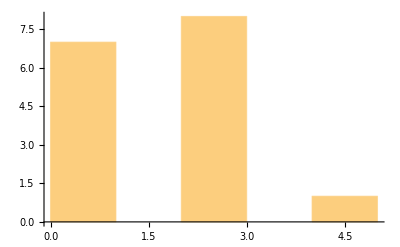

```mathematica
Histogram[{2 √2,4,2 √2,0,2,2 √2,2,0,0,0,0,0,2,2 √2,2,0}]
```

```mathematica
Abs[ExtendedWHT.ConjugateTranspose[ExtendedWHT]] // mf
```

(4 | 2 √2 | 0 | 2 √2 | 2 √2 | 2 | 0 | 2 | 0 | 0 | 0 | 0 | 2 √2 | 2 | 0 | 2
2 √2 | 4 | 2 √2 | 0 | 2 | 2 √2 | 2 | 0 | 0 | 0 | 0 | 0 | 2 | 2 √2 | 2 | 0
0 | 2 √2 | 4 | 2 √2 | 0 | 2 | 2 √2 | 2 | 0 | 0 | 0 | 0 | 0 | 2 | 2 √2 | 2
2 √2 | 0 | 2 √2 | 4 | 2 | 0 | 2 | 2 √2 | 0 | 0 | 0 | 0 | 2 | 0 | 2 | 2 √2
2 √2 | 2 | 0 | 2 | 4 | 2 √2 | 0 | 2 √2 | 2 √2 | 2 | 0 | 2 | 0 | 0 | 0 | 0
2 | 2 √2 | 2 | 0 | 2 √2 | 4 | 2 √2 | 0 | 2 | 2 √2 | 2 | 0 | 0 | 0 | 0 | 0
0 | 2 | 2 √2 | 2 | 0 | 2 √2 | 4 | 2 √2 | 0 | 2 | 2 √2 | 2 | 0 | 0 | 0 | 0
2 | 0 | 2 | 2 √2 | 2 √2 | 0 | 2 √2 | 4 | 2 | 0 | 2 | 2 √2 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 2 √2 | 2 | 0 | 2 | 4 | 2 √2 | 0 | 2 √2 | 2 √2 | 2 | 0 | 2
0 | 0 | 0 | 0 | 2 | 2 √2 | 2 | 0 | 2 √2 | 4 | 2 √2 | 0 | 2 | 2 √2 | 2 | 0
0 | 0 | 0 | 0 | 0 | 2 | 2 √2 | 2 | 0 | 2 √2 | 4 | 2 √2 | 0 | 2 | 2 √2 | 2
0 | 0 | 0 | 0 | 2 | 0 | 2 | 2 √2 | 2 √2 | 0 | 2 √2 | 4 | 2 | 0 | 2 | 2 √2
2 √2 | 2 | 0 | 2 | 0 | 0 | 0 | 0 | 2 √2 | 2 | 0 | 2 | 4 | 2 √2 | 0 | 2 √2
2 | 2 √2 | 2 | 0 | 0 | 0 | 0 | 0 | 2 | 2 √2 | 2 | 0 | 2 √2 | 4 | 2 √2 | 0
0 | 2 | 2 √2 | 2 | 0 | 0 | 0 | 0 | 0 | 2 | 2 √2 | 2 | 0 | 2 √2 | 4 | 2 √2
2 | 0 | 2 | 2 √2 | 0 | 0 | 0 | 0 | 2 | 0 | 2 | 2 √2 | 2 √2 | 0 | 2 √2 | 4)

```mathematica
Transpose[ExtendedCB]*2 // mf
```

(1 | 1 | 1 | 1
1 | -1 | 1 | -1
1 | 1 | -1 | -1
1 | -1 | -1 | 1
1 | ⅈ | 1 | ⅈ
1 | -ⅈ | 1 | -ⅈ
1 | ⅈ | -1 | -ⅈ
1 | -ⅈ | -1 | ⅈ
1 | 1 | ⅈ | ⅈ
1 | -1 | ⅈ | -ⅈ
1 | 1 | -ⅈ | -ⅈ
1 | -1 | -ⅈ | ⅈ
1 | ⅈ | ⅈ | -1
1 | -ⅈ | ⅈ | 1
1 | ⅈ | -ⅈ | 1
1 | -ⅈ | -ⅈ | -1
1 | 1 | 1 | ⅈ
1 | -1 | 1 | -ⅈ
1 | 1 | -1 | -ⅈ
1 | -1 | -1 | ⅈ
1 | ⅈ | 1 | -1
1 | -ⅈ | 1 | 1
1 | ⅈ | -1 | 1
1 | -ⅈ | -1 | -1
1 | 1 | ⅈ | -1
1 | -1 | ⅈ | 1
1 | 1 | -ⅈ | 1
1 | -1 | -ⅈ | -1
1 | ⅈ | ⅈ | -ⅈ
1 | -ⅈ | ⅈ | ⅈ
1 | ⅈ | -ⅈ | ⅈ
1 | -ⅈ | -ⅈ | -ⅈ
1 | 1 | 1 | -1
1 | -1 | 1 | 1
1 | 1 | -1 | 1
1 | -1 | -1 | -1
1 | ⅈ | 1 | -ⅈ
1 | -ⅈ | 1 | ⅈ
1 | ⅈ | -1 | ⅈ
1 | -ⅈ | -1 | -ⅈ
1 | 1 | ⅈ | -ⅈ
1 | -1 | ⅈ | ⅈ
1 | 1 | -ⅈ | ⅈ
1 | -1 | -ⅈ | -ⅈ
1 | ⅈ | ⅈ | 1
1 | -ⅈ | ⅈ | -1
1 | ⅈ | -ⅈ | -1
1 | -ⅈ | -ⅈ | 1
1 | 1 | 1 | -ⅈ
1 | -1 | 1 | ⅈ
1 | 1 | -1 | ⅈ
1 | -1 | -1 | -ⅈ
1 | ⅈ | 1 | 1
1 | -ⅈ | 1 | -1
1 | ⅈ | -1 | -1
1 | -ⅈ | -1 | 1
1 | 1 | ⅈ | 1
1 | -1 | ⅈ | -1
1 | 1 | -ⅈ | -1
1 | -1 | -ⅈ | 1
1 | ⅈ | ⅈ | ⅈ
1 | -ⅈ | ⅈ | -ⅈ
1 | ⅈ | -ⅈ | -ⅈ
1 | -ⅈ | -ⅈ | ⅈ)

Howard’s algorithm

Coordinate shifts & action of X

```mathematica
(* The permutations realizing the Howard shits are just the X-matrix acting in tensor dimension k *)
PermMatEShifts = TensorMany[Join[Table[unit2,{#}],{sigx},Table[unit2,{mm-1-#}]]] &/@ (Range[mm]-1); PermMatEShifts //mfl

(* The X-matrix acting in the first tensor dimension *)
(inx=#; avec = Table[0,{mm}]; avec[[inx]]=1; MakePauli[avec,0*avec]) &/@ Range[mm] //mfl
```

{(0 | 0 | 1 | 0
0 | 0 | 0 | 1
1 | 0 | 0 | 0
0 | 1 | 0 | 0),(0 | 1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | 1 | 0)}

{(0 | 0 | 1 | 0
0 | 0 | 0 | 1
1 | 0 | 0 | 0
0 | 1 | 0 | 0),(0 | 1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | 1 | 0)}

```mathematica
(* the binary shift vectors *)
BinaryShifts = IntegerDigits[#,2,mm] &/@ Table[Nn/2^kk,{kk,1,mm}]
(* The action of these shifts on the coordinates *)
(shift = #; FromDigits[ Mod[IntegerDigits[#-1,2,mm] + shift,2],2]+1 &/@ Range[Nn]) &/@ BinaryShifts

(* The same shifts realized by permutation matrices *)
								                           #.Range[Nn] &/@ PermMatEShifts
```

{{1,0},{0,1}}

{{3,4,1,2},{2,1,4,3}}

{{3,4,1,2},{2,1,4,3}}

```mathematica
(* The action of sum shifts on the coordinates *)
(shift =  Plus@@(BinaryShifts[[#]]); FromDigits[ Mod[IntegerDigits[#-1,2,mm] + shift,2],2]+1 &/@ Range[Nn]) &/@ {{2,1},{3,2}}
(* This is realized by sequential action of the permutation matrices *)
(* The order does not matter, as these permutators commute *)
(fir = #[[1]]; sec = #[[2]]; PermMatEShifts[[fir]].PermMatEShifts[[sec]].Range[Nn]) &/@ {{2,1},{3,2}}
```

Part::partw: Part {3,2} of {{1,0},{0,1}} does not exist.

{{4,3,2,1},{{5/4,3/2},{3/2,5/4},{3/2,2},{2,3/2}}}

Part::partw: Part 3 of {{{0,0,1,0},{0,0,0,1},{1,0,0,0},{0,1,0,0}},{{0,1,0,0},{1,0,0,0},{0,0,0,1},{0,0,1,0}}} does not exist.

{{4,3,2,1},{{{0,0,1,0},{0,0,0,1},{1,0,0,0},{0,1,0,0}},{{0,1,0,0},{1,0,0,0},{0,0,0,1},{0,0,1,0}}}⟦3⟧.{2,1,4,3}}

{BinaryChirp,Smat} = HowardEnforcingS[vec]

```mathematica
(* enforces the S-matrix to be symmetric *)
```

```mathematica
(*
HowardEnforcingS = Module[{vecin,RM2funShiftProd,WHshifts,AbsWHsh,inx,start,range,RangeNow,abses,maxi,posi,Sest,phi0,bvec,dechirpWH,best,vecest},
vecin = #; 
(* Howard algorithm for decoding S-matrix *)
RM2funShiftProd = Nn*Conjugate[vecin]*(#.vecin) &/@ PermMatEShifts;
(* Partial WH-transforms of these *)
WHshifts = RM2funShiftProd.WHn;
AbsWHsh = Abs[WHshifts];


(* the S estimate, enforced to be symmetric *)
Sest = Table[0,{mm},{mm}];
(inx = #; 
 start = Transpose[Sest][[inx]];
range = 2^(mm+1-inx);
(* reduce the range now such that the result is forced to be symmetric *)
RangeNow = FromDigits[start,2]+Range[range];
(*Print[StringForm["RangeNow normal ``.", RangeNow]];*)
(* The absolute WH of the shift results now *)
abses = AbsWHsh[[inx]];
(* the max is chosen from the limited set, commensurate with symmetric S *)
maxi  = Max[abses[[RangeNow]]];
posi = Position[abses,maxi][[1,1]];
Sest[[inx]]=IntegerDigits[posi-1,2,mm]; 
) &/@ Range[mm];
(*Print[Sest // mf];*)

(* now estimate the b-vector *)
(* Dechirp with estimated S, and *Partial* WH-transform, Howard's algorithm  *)
phi0 = (bvec = IntegerDigits[#-1,2,mm]; I^(bvec.Sest.bvec)) &/@ Range[Nn];
dechirpWH = Abs[DiscreteHadamardTransform[tstvec *phi0,Method->"BitComplement"]];
best = IntegerDigits[Position[dechirpWH,Max[dechirpWH]][[1,1]]-1,2,mm];
vecest = (cvec = IntegerDigits[#-1,2,mm];(-I)^(cvec.Sest.cvec + 2*best.cvec)) &/@ Range[Nn]; vecest  = vecest/Norm[vecest];
{vecest,Sest}
]&;
*)
```

DecodeRow

```mathematica
DecodeRow = Module[{vecin, mu, Sest, signbits, tt, r, K, start, RangeNow, newK, wht, abses, signs, metrics, signbitsall, projectedvectors, Sests, peaks, peak, Sestk, metrick , PhaseVec, sigmak, signbitsk, Svec, avec, bvec, X, vecrot, veck, results, PermMatEsh, peaki, withProjections}, 
Sest = #[[1]];
vecin = #[[2]];
signbits = #[[3]];
mu = #[[4]];
tt = #[[5]];
r = #[[6]];
K = #[[7]];
withProjections = #[[8 ]];

start = Transpose[Sest][[r]];
RangeNow=Pick[Range[2^mm],tt] + FromDigits[start,2];
(* In the end K might be greater than the number of possible different rows *)
newK = Min[K, Length[RangeNow]];

(* Note: For precise correspondence as real number, one has to multiply with these! *)
avec = ZeroVecm; avec[[r]]=1;
(* TODO ad-hoc phasevec, find out the reason why this works *)
PhaseVec = (bvec = IntegerDigits[#-1,2,mm]; I^(avec.bvec)) &/@Range[Nn]  //Chop;

PermMatEsh =  PermMatEShifts[[r]];
wht =  Sqrt[Nn]PhaseVec*(Conjugate[vecin]*(PermMatEsh.vecin)).WHn // Chop;
abses = Abs[wht];
signs = Sign[wht];

metrics = {};
signbitsall = {};
projectedvectors = {};
Sests = {};

(* peaks = Reverse[Ordering[abses]]; *)
(* improve peaki computation maybe without comparisons *)
peaks = Reverse[Sort[abses[[RangeNow]]]];
results = {};
(k=#;
peaki = Position[abses,peaks[[k]]][[1,1]];
(* peak = peaks[[k]]; *)
(* Mathematica copies arrays by default so no worries of reference problems *)
Sestk = Sest;

If[withProjections, metrick = (mu + abses[[peaki]]) / 2;, metrick = (mu + abses[[peaki]]);];
(* May give wrong result *)
sigmak = signs[[peaki]];

signbitsk = signbits; 
signbitsk[[r]] =(1 + sigmak) / 2;

Svec  = IntegerDigits[peaki-1,2,mm];
Sestk[[r]]=Svec;


If[withProjections, avec = ZeroVecm; avec[[r]]=1;
(* construct the  Pauli found, the sought for codeword is an eigenvector of this Pauli with eigenvalue +- 1  *)
X = MakePauli[avec,Svec];
vecrot = X.vecin;
veck = (vecin + sigmak * vecrot) / 2;, 
(* This runs if withProjections = False *)
veck = vecin;];

results = Append[results, {Sestk, veck, signbitsk, metrick}];
) &/@ Range[newK];
results
]&;
```

```mathematica
BreadthFirstDecoding = Module[{vecin, ordering, tt, Sest, K, candidatelist, newcandidates, r, inx, jnx, metrics, peakinxs, withProjections}, vecin = #[[1]]; ordering = #[[2]]; K = #[[3]];withProjections = #[[4]];
tt = Table[True, 2^mm];
Sest = Table[0,{mm},{mm}];
candidatelist = {{Table[0,{mm},{mm}], vecin, Table[0, mm], Norm[vecin]^2}};
(inx = #;
newcandidates = {};
r = ordering[[inx]];
(jnx = #;
(* FOR FUTURE DEVELOPEMENT: If ordering is modified during the run, this needs to be improved *)
newcandidates = Join[newcandidates,DecodeRow[Join[candidatelist[[jnx]],{tt, r, K, withProjections}]]];
)&/@Range[Length[candidatelist]];
metrics = {};
(* TODO optimize *)
(jnx = #; metrics = Append[metrics, newcandidates[[jnx,4]]];) &/@Range[Length[newcandidates]];
peakinxs = Reverse[Ordering[metrics]];
candidatelist = {};
(* TODO optimize *)
(jnx = #; candidatelist = Append[candidatelist, newcandidates[[peakinxs[[jnx]]]]];)&/@Range[Min[K, Length[newcandidates]]];
tt = UpdateTruthTable[{GiveTruthTable[{r, mm}], tt}];
)&/@ Range[mm];


If[withProjections, posi = 1, inners = (best = #[[3]]; best = 1 - best; Sest = #[[1]];
vecest = (cvec = IntegerDigits[#-1,2,mm];(-I)^(cvec.Sest.cvec + 2*best.cvec)) &/@ Range[Nn]; vecest  = vecest/Norm[vecest];
Abs[Conjugate[tstvec].vecest]
) &/@ candidatelist;

posi = Position[inners,Max[inners]][[1,1]]; ];
candidatelist[[posi]]
]&;
```

```mathematica
DecodingOrder = Module[{vecin, maxis, PermMatEsh, abses, permutetable}, vecin = #;
maxis = {};
(inx = #;
	PermMatEsh =  PermMatEShifts[[inx]];
	abses = Abs[ Nn*(Conjugate[vecin]*(PermMatEsh.vecin)).WHn];
	maxis  = Append[maxis, Max[abses]];
) &/@ Range[mm];
Reverse[Ordering[maxis]]
]&;
```

{BinaryChirp,Smat} = HowardPermuteEnforcingS[vec]

```mathematica
GiveTruthTable = Module[{index, size, basetable, binary}, input=#;
index = #[[1]];
size = #[[2]];
binary = Mod[Floor[(Range[2^size] - 1) / 2^(size -index)], 2];
Table[binary[[i]] == 0, {i, 1, 2^size}]
]&;
UpdateTruthTable = Module[{tt1, tt2}, input = #;
tt1 = #[[1]];
tt2 = #[[2]];
Table[tt1[[i]] && tt2[[i]], {i, 1, Length[tt1]}]
]&;
(*
HowardPermuteEnforcingS = Module[{vecin,RM2funShiftProd,WHshifts,AbsWHsh,inx,start,range,RangeNow,abses,maxi,posi,Sest,phi0,bvec,dechirpWH,best,vecest},
vecin = #; 
(* Howard algorithm for decoding S-matrix *)
RM2funShiftProd = Nn*Conjugate[vecin]*(#.vecin) &/@ PermMatEShifts;
(* Partial WH-transforms of these *)
WHshifts = RM2funShiftProd.WHn;
AbsWHsh = Abs[WHshifts];
tt = Table[True, 2^mm];

(* the S estimate, enforced to be symmetric *)
Sest = Table[0,{mm},{mm}];

maxis = {};
(inx = #;
	abses = AbsWHsh[[inx]];
	maxis  = Append[maxis, Max[abses]];
) &/@ Range[mm];
permutetable = Reverse[Ordering[maxis]];


(inx = #; 
permuteinx = permutetable[[inx]];
start = Transpose[Sest][[permuteinx]];
range = 2^(mm+1-inx);
(* reduce the range now such that the result is forced to be symmetric *)
RangeNow=Pick[Range[2^mm],tt] + FromDigits[start,2];
(* The absolute WH of the shift results now *)
abses = AbsWHsh[[permuteinx]];
(* the max is chosen from the limited set, commensurate with symmetric S *)
maxi  = Max[abses[[RangeNow]]];
posi = Position[abses,maxi][[1,1]];
Sest[[permuteinx]]=IntegerDigits[posi-1,2,mm];
tt = UpdateTruthTable[{GiveTruthTable[{permuteinx, mm}], tt}];
) &/@ Range[mm];

(* now estimate the b-vector *)
(* Dechirp with estimated S, and *Partial* WH-transform, Howard's algorithm  *)
phi0 = (bvec = IntegerDigits[#-1,2,mm]; I^(bvec.Sest.bvec)) &/@ Range[Nn];
dechirpWH = Abs[DiscreteHadamardTransform[tstvec *phi0,Method->"BitComplement"]];
best = IntegerDigits[Position[dechirpWH,Max[dechirpWH]][[1,1]]-1,2,mm];
vecest = (cvec = IntegerDigits[#-1,2,mm];(-I)^(cvec.Sest.cvec + 2*best.cvec)) &/@ Range[Nn]; vecest  = vecest/Norm[vecest];
{vecest,Sest}
]&;
*)
```

{BinaryChirp,Smat} = HowardEnforceSprojOut[vec]  (NOTE: the dechirping may be redundant)

```mathematica
(* note: the eigenvectors of the m found paulis should completely characterize the codeword, the dechirping phase shouls not be needed! *)
```

```mathematica
(* enforces the S-matrix to be symmetric *)
(* After estimating each row of the S-matrix, finds wheteher the codeword of interst is eigenvalue 1 or -1 w.r.t. to found Pauli, and projects out the other part  *)
```

```mathematica
HowardEnforceSprojOut = Module[{vecin,RM2funShiftProd,WHshifts,AbsWHsh,inx,start,range,RangeNow,abses,maxi,posi,Sest,phi0,bvec,dechirpWH,best,vecest},
vecin = #; 

(* find the S estimate, enforced to be symmetric *)
Sest = Table[0,{mm},{mm}];
SignSet = {};

(inx = #; 
(* The absolute WH of the shift results now *)
PermMatEsh =  PermMatEShifts[[inx]];
abses = Abs[ Nn*(Conjugate[vecin]*(PermMatEsh.vecin)).WHn]; 
 start = Transpose[Sest][[inx]];
range = 2^(mm+1-inx);
(* reduce the range now such that the result is forced to be symmetric *)
RangeNow = FromDigits[start,2]+Range[range];
(* the max is chosen from the limited set, commensurate with symmetric S *)
maxi  = Max[abses[[RangeNow]]];
posi = Position[abses,maxi][[1,1]];
Svec = IntegerDigits[posi-1,2,mm];
Sest[[inx]]=Svec; 

avec = ZeroVecm; avec[[inx]]=1;
(* construct the  Pauli found, the sought for codeword is an eigenvector of this Pauli with eigenvalue +- 1  *)
X = MakePauli[avec,Svec];
(* act with the Pauli on the quantized vector *)
vecrot = X.vecin;
(* the reults from projecting out either the + or - eigenspace *)
vecPlus = (vecin + vecrot)/2;
vecMinus = (vecin - vecrot)/2;
If[Norm[vecPlus]>Norm[vecMinus], vecin = vecPlus; AppendTo[SignSet,1], vecin = vecMinus; AppendTo[SignSet,-1]];
) &/@ Range[mm];
(* now estimate the b-vector *)
(* Dechirp with estimated S, and *Partial* WH-transform, Howard's algorithm  *)
phi0 = (bvec = IntegerDigits[#-1,2,mm]; I^(bvec.Sest.bvec)) &/@ Range[Nn];
dechirpWH = Abs[DiscreteHadamardTransform[tstvec *phi0,Method->"BitComplement"]];
best = IntegerDigits[Position[dechirpWH,Max[dechirpWH]][[1,1]]-1,2,mm];
vecest = (cvec = IntegerDigits[#-1,2,mm];(-I)^(cvec.Sest.cvec + 2*best.cvec)) &/@ Range[Nn]; vecest  = vecest/Norm[vecest];
{vecest,Sest}
]&;
```

{BinaryChirp,Smat} = HowardPermuteEnforceSprojOut[vec]  (NOTE: the dechirping may be redundant)

```mathematica
(*
HowardPermuteEnforceSprojOut = Module[{vecin,RM2funShiftProd,WHshifts,AbsWHsh,inx,start,range,RangeNow,abses,maxi,posi,Sest,phi0,bvec,dechirpWH,best,vecest},
vecin = #; 

(* find the S estimate, enforced to be symmetric *)
Sest = Table[0,{mm},{mm}];
SignSet = {};

tt = Table[True, 2^mm];
maxis = {};
(inx = #;
	PermMatEsh =  PermMatEShifts[[inx]];
	abses = Abs[ Nn*(Conjugate[vecin]*(PermMatEsh.vecin)).WHn];
	maxis  = Append[maxis, Max[abses]];
) &/@ Range[mm];
permutetable = Reverse[Ordering[maxis]];

(inx = #; 
permuteinx = permutetable[[inx]];
(* The absolute WH of the shift results now *)
PermMatEsh =  PermMatEShifts[[permuteinx]];
abses = Abs[ Nn*(Conjugate[vecin]*(PermMatEsh.vecin)).WHn]; 
start = Transpose[Sest][[permuteinx]];
(* reduce the range now such that the result is forced to be symmetric *)
RangeNow=Pick[Range[2^mm],tt] + FromDigits[start,2];
(* the max is chosen from the limited set, commensurate with symmetric S *)
maxi  = Max[abses[[RangeNow]]];
posi = Position[abses,maxi][[1,1]];
Svec = IntegerDigits[posi-1,2,mm];
Sest[[permuteinx]]=Svec; 

avec = ZeroVecm; avec[[permuteinx]]=1;
(* construct the  Pauli found, the sought for codeword is an eigenvector of this Pauli with eigenvalue +- 1  *)
X = MakePauli[avec,Svec];
(* act with the Pauli on the quantized vector *)
vecrot = X.vecin;
(* the reults from projecting out either the + or - eigenspace *)
vecPlus = (vecin + vecrot)/2;
vecMinus = (vecin - vecrot)/2;
If[Norm[vecPlus]>Norm[vecMinus], vecin = vecPlus; AppendTo[SignSet,1], vecin = vecMinus; AppendTo[SignSet,-1]];
tt = UpdateTruthTable[{GiveTruthTable[{permuteinx, mm}], tt}];

) &/@ Range[mm];

(* now estimate the b-vector *)
(* Dechirp with estimated S, and *Partial* WH-transform, Howard's algorithm  *)
phi0 = (bvec = IntegerDigits[#-1,2,mm]; I^(bvec.Sest.bvec)) &/@ Range[Nn];
dechirpWH = Abs[DiscreteHadamardTransform[tstvec *phi0,Method->"BitComplement"]];
best = IntegerDigits[Position[dechirpWH,Max[dechirpWH]][[1,1]]-1,2,mm];
vecest = (cvec = IntegerDigits[#-1,2,mm];(-I)^(cvec.Sest.cvec + 2*best.cvec)) &/@ Range[Nn]; vecest  = vecest/Norm[vecest];
{vecest,Sest}
]&;
*)
```

```mathematica
(* find closest codeword to random vector *)
(*
tstvec = {1,I}.RandomVariate[NormalDistribution[0,1],{2,Nn}]; tstvec = tstvec/Norm[tstvec];
inners = Abs[Conjugate[tstvec].CB];
posi = Position[inners,Max[inners]][[1,1]];
Dist2closest = 1-inners[[posi]]^2

(* The Howard enforcing symmetry of S *)
{vecest,Sest} = HowardEnforcingS[tstvec];
1-Abs[Conjugate[tstvec].vecest]^2 - Dist2closest

(* The Howard permuted enforcing symmetry of S *)
{vecest,Sest} = HowardPermuteEnforcingS[tstvec];
1-Abs[Conjugate[tstvec].vecest]^2 - Dist2closest 

(* Enforcing symmetry of S, and projecting out smaller eigenvalue half-space in each stage   *)
{vecest,Sest} = HowardEnforceSprojOut[tstvec];
1-Abs[Conjugate[tstvec].vecest]^2 - Dist2closest

(* Permuted, Enforcing symmetry of S, and projecting out smaller eigenvalue half-space in each stage *)
{vecest,Sest} = HowardPermuteEnforceSprojOut[tstvec];
1-Abs[Conjugate[tstvec].vecest]^2 - Dist2closest 

*)
```

```mathematica
(*
ChordStore = {};
FoundClosestStore = {};
drops =10000; CountZero = 0;
drops = 0;

(If[Mod[CountZero++,500]==0,PrintTemporary[CountZero-1]];
(* find closest codeword to random vector *)
tstvec = {1,I}.RandomVariate[NormalDistribution[0,1],{2,Nn}]; tstvec = tstvec/Norm[tstvec];

ChordDists = Table[0,{6}];
FoundClosest = Table[0,{5}];

inners = Abs[Conjugate[tstvec].CB];
posi = Position[inners,Max[inners]][[1,1]];
ConjClosestVec = Conjugate[Transpose[CB][[posi]]];
Dist2 = 1-inners[[posi]]^2;
ChordDists[[1]]=Sqrt[Dist2];

(* The Howard enforcing symmetry of S *)
{vecest,Sest} = HowardEnforcingS[tstvec];
Dist2 = 1-Abs[Conjugate[tstvec].vecest]^2 ;
FoundClosest[[1]]= If[Abs[ConjClosestVec.vecest]> 0.99,1,0];
ChordDists[[2]]=Sqrt[Dist2];

(* The Howard permuted enforcing symmetry of S *)
{vecest,Sest} = HowardPermuteEnforcingS[tstvec];
Dist2 = 1-Abs[Conjugate[tstvec].vecest]^2 ;
FoundClosest[[2]]= If[Abs[ConjClosestVec.vecest]> 0.99,1,0];
ChordDists[[3]]=Sqrt[Dist2];

(* Enforcing symmetry of S, and projecting out smaller eigenvalue half-space in each stage   *)
{vecest,Sest} = HowardEnforceSprojOut[tstvec];Sest //mf;
Dist2 = 1-Abs[Conjugate[tstvec].vecest]^2 ;
FoundClosest[[3]]= If[Abs[ConjClosestVec.vecest]> 0.99,1,0];
ChordDists[[4]]=Sqrt[Dist2];

(* Permuted, Enforcing symmetry of S, and projecting out smaller eigenvalue half-space in each stage   *)
{vecest,Sest} = HowardPermuteEnforceSprojOut[tstvec];Sest //mf;
Dist2 = 1-Abs[Conjugate[tstvec].vecest]^2 ;
FoundClosest[[4]]= If[Abs[ConjClosestVec.vecest]> 0.99,1,0];
ChordDists[[5]]=Sqrt[Dist2];


(* Breadth first *)   
{Sest, zleft, best, metric} = BreadthFirstDecoding[{tstvec, {1,2,3}, 64, False}];Sest //mf;
(* TODO: ASK IS THIS COMPLEMENT ?? *)
best = 1 - best;
vecest = (cvec = IntegerDigits[#-1,2,mm];(-I)^(cvec.Sest.cvec + 2*best.cvec)) &/@ Range[Nn]; vecest  = vecest/Norm[vecest];

Dist2 = 1-Abs[Conjugate[tstvec].vecest]^2 ;
FoundClosest[[5]]= If[Abs[ConjClosestVec.vecest]> 0.99,1,0];
ChordDists[[6]]=Sqrt[Dist2];


AppendTo[ChordStore,ChordDists];
AppendTo[FoundClosestStore,FoundClosest];
) &/@ Range[drops];

meanC = Mean[ChordStore]
meanPe = Mean[FoundClosestStore] //N
Abs[1-#/meanC[[1]]] &/@ meanC

*)
```

```mathematica
drops =1; CountZero = 0;
res = {};
Ktable = Join[{1},Range[2,Nn,6]];(*Range[1,Nn,2];*)(*Range[15];{1,5,10,15};*)

ChordStore = {};
FoundClosestStore = {};
(If[Mod[CountZero++,500]==0,PrintTemporary[CountZero-1]];
(* find closest codeword to random vector *)
tstvec = {1,I}.RandomVariate[NormalDistribution[0,1],{2,Nn}]; tstvec = tstvec/Norm[tstvec];

ChordDists = Table[0,{5}];
FoundClosest = Table[0,{4}];

inners = Abs[Conjugate[tstvec].CB];
posi = Position[inners,Max[inners]][[1,1]];
ConjClosestVec = Conjugate[Transpose[CB][[posi]]];
DistOrig = 1-inners[[posi]]^2;
ChordDists[[1]]=Sqrt[Dist2];

(K = #;
ChordDists = Table[0,{5}];
FoundClosest = Table[0,{4}];
ChordDists[[1]]=Sqrt[DistOrig];

(* Breadth first depth mm fixed order *)   
{Sest, zleft, best, metric} = BreadthFirstDecoding[{tstvec, Range[mm], K, False}];Sest //mf;
(* TODO: ASK IS THIS COMPLEMENT ?? *)
best = 1 - best;
vecest = (cvec = IntegerDigits[#-1,2,mm];(-I)^(cvec.Sest.cvec + 2*best.cvec)) &/@ Range[Nn]; vecest  = vecest/Norm[vecest];

Dist2 = 1-Abs[Conjugate[tstvec].vecest]^2 ;
FoundClosest[[1]]= If[Abs[ConjClosestVec.vecest]> 0.99,1,0];
ChordDists[[2]]=Sqrt[Dist2];

(* Breadth first depth mm fixed order w projections *)   
{Sest, zleft, best, metric} = BreadthFirstDecoding[{tstvec, Range[mm], K, True}];Sest //mf;
(* TODO: ASK IS THIS COMPLEMENT ?? *)
best = 1 - best;
vecest = (cvec = IntegerDigits[#-1,2,mm];(-I)^(cvec.Sest.cvec + 2*best.cvec)) &/@ Range[Nn]; vecest  = vecest/Norm[vecest];

Dist2 = 1-Abs[Conjugate[tstvec].vecest]^2 ;
FoundClosest[[2]]= If[Abs[ConjClosestVec.vecest]> 0.99,1,0];
ChordDists[[3]]=Sqrt[Dist2];

(* Breadth first depth mm permuted order *)   
{Sest, zleft, best, metric} = BreadthFirstDecoding[{tstvec, DecodingOrder[tstvec], K, False}];Sest //mf;
(* TODO: ASK IS THIS COMPLEMENT ?? *)
best = 1 - best;
vecest = (cvec = IntegerDigits[#-1,2,mm];(-I)^(cvec.Sest.cvec + 2*best.cvec)) &/@ Range[Nn]; vecest  = vecest/Norm[vecest];

Dist2 = 1-Abs[Conjugate[tstvec].vecest]^2 ;
FoundClosest[[3]]= If[Abs[ConjClosestVec.vecest]> 0.99,1,0];
ChordDists[[4]]=Sqrt[Dist2];

(* Breadth first depth mm pertmuted order w projections *)   
{Sest, zleft, best, metric} = BreadthFirstDecoding[{tstvec, DecodingOrder[tstvec], K, True}];Sest //mf;
(* TODO: ASK IS THIS COMPLEMENT ?? *)
best = 1 - best;
vecest = (cvec = IntegerDigits[#-1,2,mm];(-I)^(cvec.Sest.cvec + 2*best.cvec)) &/@ Range[Nn]; vecest  = vecest/Norm[vecest];

Dist2 = 1-Abs[Conjugate[tstvec].vecest]^2 ;
FoundClosest[[4]]= If[Abs[ConjClosestVec.vecest]> 0.99,1,0];
ChordDists[[5]]=Sqrt[Dist2];

AppendTo[ChordStore,ChordDists];
AppendTo[FoundClosestStore,FoundClosest];
) &/@Ktable;


) &/@ Range[drops];
(* TODO improve the data structures somehow that this one below is not deeded *)
(inx = #;
chordstoreinx = {};
foundcloseststoreinx = {};
(jnx = #; chordstoreinx = Append[chordstoreinx, ChordStore[[inx + Length[Ktable] * (jnx-1)]]])&/@Range[drops];
(jnx = #; foundcloseststoreinx = Append[foundcloseststoreinx, FoundClosestStore[[inx + Length[Ktable] * (jnx-1)]]])&/@Range[drops];
meanC = Mean[chordstoreinx];
meanPe = Mean[foundcloseststoreinx] //N;
res = Append[res, {Ktable[[inx]], meanC, meanPe, Abs[1-#/meanC[[1]]] &/@ meanC}];

) &/@Range[Length[Ktable]]; 

Print[res];
(*
outputfile = OpenWrite["C:/Users/heikkie13/howard/mfivelongsimu.txt"];
Write[outputfile, res];
Close[outputfile];
*)
```

{{1,{0.515504,0.515504,0.515504,0.515504,0.515504},{1.,1.,1.,1.},{0.,4.44089×10^-16,4.44089×10^-16,4.44089×10^-16,4.44089×10^-16}},{2,{0.515504,0.515504,0.515504,0.515504,0.515504},{1.,1.,1.,1.},{0.,4.44089×10^-16,4.44089×10^-16,4.44089×10^-16,4.44089×10^-16}}}